```mathematica
SetDirectory[NotebookDirectory[]];
```

## 首先钦定一个和弦进行

```mathematica
Music[s_]:=MusicCreate@SMSPCompile[StringJoin["<<chords.txt\n m[4,120,0]\n",s]]
```

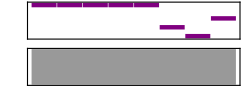

```mathematica
Music["[P] i[Midi[Piano]] v[1]
[P] (0) ^1---|^1---|^1---|^1---|
^1---|5---|4---|6---|"]
```

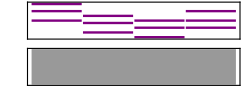

```mathematica
Music["[P] i[Midi[Piano]] v[1]
[P] (0) |"<>
StringJoin[#1<>">s---|"&/@{"^C","G","F","Am"}]]
```

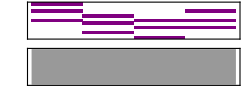

```mathematica
Music["[P] i[Midi[Piano]] v[1]
[P] (0) |"<>
StringJoin[#1<>">s s s s|"&/@{"^C","G","F","Am"}]]
```

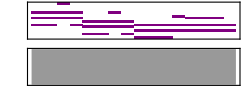

```mathematica
Music["[P] i[Midi[Piano]] v[1]
[P] (0) |"<>
StringJoin[#1<>">s s_ s_ u s|"&/@{"^C","G"},
"F>s s_ s_ s_ s_ u|Am>s s_ s_ s ab|"]]
```

## 详见 AlphaTexture

构建 C 大调白键和弦表，按｛根音，三音，五音，七音，九音｝排序

```mathematica
Major={0,4,7,11,14}; (* 大九和弦 *)
Minor={0,3,7,10,14}; (* 小九和弦 *)
Clist={
(* C *) Major,
(* Dm *) Minor+2,
(* Em *) Minor+4,
(* F *) Major+5,
(* G *) Major+7,
(* Am *) Minor+9,
(* Bdim *) {0,3,6,10,13}+11
};
(* 扩充一遍升八度的 *)
Clist=Join[Clist,Clist+12];
```

将左右手钢琴封装成织体模块，接收参数为和弦进行、左右手节奏型（表）

```mathematica
PianoLR[cp_,lepat_,ripat_]:=Module[{left,righ},
left=StringJoin[Table[{
StringReplace[ToString[Clist⟦cp⟦i⟧,1;;3⟧],{" "->"","{"->"<","}"->"> "}],
lepat⟦i⟧},{i,1,Length[cp]}]];
righ=StringJoin[Table[{
StringReplace[ToString[Clist⟦cp⟦i⟧⟧],{" "->"","{"->"<","}"->"> "}],
ripat⟦i⟧},{i,1,Length[cp]}]];
Return["\n[left] i[Midi[Piano,-12]] v[.1]
[righ] i[Midi[Piano]] v[.08]
[left] (0) "<>left<>"\n"<>
"[righ] (0) "<>righ]
]
```

```mathematica
(* 重复 *)
r[s_,time_]:=StringJoin[Table[s,{time}]]
```

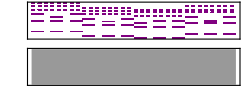

```mathematica
Music@PianoLR[{8,5,4,6},{"sa 0_ sb 0_ sa| ","sa 0_ sb 0_ sa| ","sb 0_ sa 0_ sa| ","sa 0_ sb 0_ sa| "},Table[r["r= 0= ",8]<>" | ",{4}]]
```

## 详见 AlphaBeat

函数封装，接收参数：drum、hat、tom（分别带起始小节号）

```mathematica
Beat[nd_,d_,nh_,h_]:=StringJoin["\n
<<beats.txt
[drum] i[Midi[]] v[.5]
[hat] i[Midi[]] v[.3]
[drum] (",ToString[nd],") ",d,"
[hat] (",ToString[nh],") ",h]
```

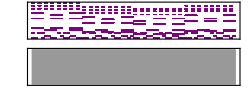

```mathematica
Music[{PianoLR[{8,5,4,6},{"sa 0_ sb 0_ sa| ","sa 0_ sb 0_ sa| ","sb 0_ sa 0_ sa| ","sa 0_ sb 0_ sa| "},Table[r["r= 0= ",8]<>" | ",{4}]],
Beat[0,StringJoin[
"M_ 0= M= S_ M_ 0= S= M_ S_ M_ |",
"M_ 0= M= S_ M_ 0= S= M_ S= S= M= S=|",
"M_ 0= M= S_ M_ 0= S= M_ S_ M_ |",
"M_ 0= M= S_ M_ 0= S= M_ S= S= M= S=|"
],0,r[{r["T= 0= T= T= To ",2],"|"},4]]
}]
```

```mathematica
BassR[cp_,ripat_]:=Module[{righ},
righ=StringJoin[Table[{
StringReplace[ToString[Clist⟦cp⟦i⟧⟧],{" "->"","{"->"<","}"->"> "}],
ripat⟦i⟧},{i,1,Length[cp]}]];
Return["\n[bass] i[Midi[Bass,-24]] v[1]
[bass] (0) "<>righ]
]
```

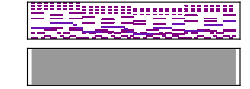

```mathematica
Music[{PianoLR[{8,5,4,6},{"sa 0_ sb 0_ sa| ","sa 0_ sb 0_ sa| ","sb 0_ sa 0_ sa| ","sa 0_ sb 0_ sa| "},Table[r["r= 0= ",8]<>" | ",{4}]],
Beat[0,StringJoin[
"M_ 0= M= S_ M_ 0= S= M_ S_ M_ |",
"M_ 0= M= S_ M_ 0= S= M_ S= S= M= S=|",
"M_ 0= M= S_ M_ 0= S= M_ S_ M_ |",
"M_ 0= M= S_ M_ 0= S= M_ S= S= M= S=|"
],0,r[{r["T= 0= T= T= To ",2],"|"},4]],
BassR[{8,5,4,6},Join[Table["a_= a_= c_= c_= c= b= a_| ",{2}],Table["a_= a_= c_= c_= ^a_ ^a_| ",{2}]]]
}]
```

## 详见 AlphaMain

```mathematica
Main[cp_,ripat_]:=Module[{righ},
righ=StringJoin[Table[{
StringReplace[ToString[Clist⟦cp⟦i⟧⟧],{" "->"","{"->"<","}"->"> "}],
ripat⟦i⟧},{i,1,Length[cp]}]];
Return["\n[flute] i[Midi[Flute]] v[1]
[flute] (0) "<>righ]
]
```

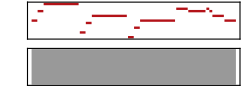

```mathematica
Music@Main[{8,5,4,6},Join[Table["a_ b_ c--| ",{3}],Table["#c c. #c= c=  ##b b | ",{2}]]]
```

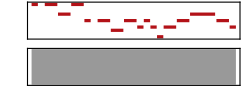

```mathematica
Music@Main[{8,5,4,6},Join[Table["c_ 0_ c b c| ",{2}],{"c_ ##c_ c_ b_ c ##c | ","c- ##b b_|"}]]
```

## 点缀库

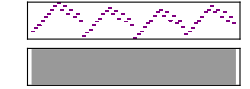

```mathematica
Music@PianoLR[{8,5,4,6},Table["|",{4}],Table["a= b= c= ^a= ^b= ^c= ^^a= ^^b= ^^c= ^^a= ^^b= ^c= ^^a= ^b= ^c= ^a= ",{4}]]
```

## SMSP 汇总

```mathematica
Music[s_]:=(OutputForm[s<>"\n"]>>>"music.txt";MusicCreate@SMSPCompile[StringJoin["<<chords.txt\n m[4,140,0]\n",s]]
)
```

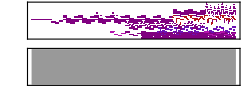

```mathematica
MusicCreate@SMSPCompile[Import["music.txt"]]
```

```mathematica
Export["music.mid",%50]
```

music.mid